# Spectral analysis for transport

## First spectral density

Anti-symmetrized Lorentzian

```mathematica
Clear[jj];
(*
	γ: "damping rate"/width parameter;
	Ω: center;
	λ: sys-env coupling strength
*)
jj[γ_,Ω_,λ_][x_] =λ^2/π(1/(γ^2+(x-Ω)^2) -1/(γ^2+(x+Ω)^2)) ;
```

Thermalized SD

```mathematica
(*temp: temperature*)
(*units hbar/kB*)
Clear[temp];
temp = 150;
```

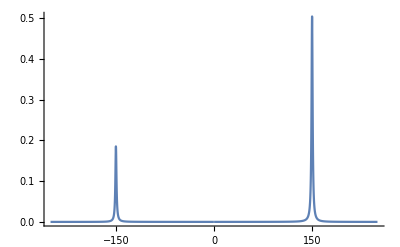

```mathematica
Plot[1/2(1+Coth[x/2 1/temp])jj[1,150,1][x],{x,-250,250},PlotRange->All]
```

System-chain coupling coefficient (κ_0)

## Spin chain

Single excitation subspace (N=1): from this we can derive the eigen-energies and the eigen-states by means of suitable operations (sum) and tranformations (Slater Determinant)

The relation between momentum-energy-velocity is well known for discretized systems. 
Question: what would happen if the couplings/frequencies were not uniform?

```mathematica
Clear[eigenValues,eigenVectors,velocities];
eigenValues[ϵ_,κ_][s_][k_]:=ϵ - 2 κ Cos[(k π)/(s+1)]
eigenVectors[ϵ_,κ_][s_][k_][x_]:=√(1/(s+1)) Sin[(k π x)/(s+1)]
```

```mathematica
velocities[ϵ_,κ_][s_][k_]:=D[ϵ - 2 κ Cos[(ζ π)/(s+1)],ζ]/.ζ->k
```

```mathematica
Table[eigenValues[150,1][10][i],{i,10}]//N
```

{148.081,148.317,148.69,149.169,149.715,150.285,150.831,151.31,151.683,151.919}

```mathematica
Table[momenta[150,1][10][i],{i,10}]//N
```

{0.160925,0.308813,0.431683,0.519581,0.565385,0.565385,0.519581,0.431683,0.308813,0.160925}

```mathematica
D[ϵ - 2 κ Cos[(ζ π)/(s+1)],ζ]
```

(2 π κ Sin[(π ζ)/(1+s)])/(1+s)

0< v < (2π κ)/(s+1)

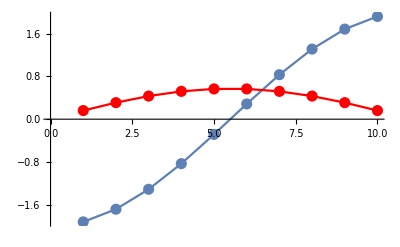

```mathematica
Show[
ListPlot[Table[eigenValues[0,1][10][i],{i,10}],Joined->True],
ListPlot[Table[eigenValues[0,1][10][i],{i,10}],PlotStyle->PointSize[0.02]],
ListPlot[Table[momenta[0,1][10][i],{i,10}],Joined->True,PlotStyle->Red],
ListPlot[Table[momenta[0,1][10][i],{i,10}],PlotStyle->{Red,PointSize[0.02]}]
]
```

First component of each of the single excitation eigenvectors.

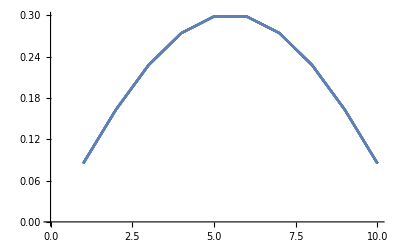

```mathematica
Show[
Table[
ListPlot[Table[eigenVectors[150,1][10][i][1],{i,10}],Joined->True],{k,1,10}]]
```

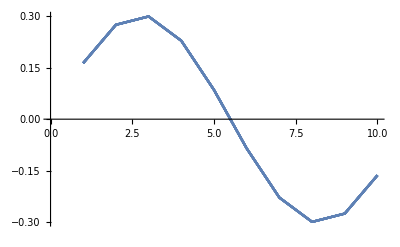

```mathematica
Show[
Table[
ListPlot[Table[eigenVectors[150,1][10][i][2],{i,10}],Joined->True],{k,1,10}]]
```